# Lab 02 : Electric Fields of Various Electrode Geometries

Charlie Bushman
Phys 235 Lab 02
04-09-19

```mathematica
Needs["ErrorBarPlots`"]
```

## Section A : Parallel Plate Capacitor

Using two flat parallel electrodes, we will find the charge on them for given input voltages. The voltages will be supplied by a function generator set to 16 kHz and the output voltages from the parallel plate capacitor is amplified then measured by an oscilloscope.

### Section A .1 : Amplifier Proportionality Constant

The amplifier we are using has a unique proportionality constant (in the realm of 0.08 V output for 1pC input charge) which we must determine before using the amplifier. To do this, we use a series of test capacitors of known capacitances (1 pF to 22 pF) and measure output voltages for a constant input voltage. This gives us the data in capFxnVoltAmpVolt below and allows us to find the proportionality constant of the amplifier.

```mathematica
(*Table 1*)
(*Note the reordering: Capacitance, Subscript[V, fg], Subscript[V, a]*)
capFxnVoltAmpfVolt={{22*10^-12,3.68,7.36},{15*10^-12,3.68,5.04},{10*10^-12,3.68,3.36},{5*10^-12,3.68,1.88},{2*10^-12,3.68,0.728},{1*10^-12,3.68,0.396}};
capFxnVoltAmpfVolt//N//TableForm
(*Table 3*)
chrgAmpfVolt=Table[{capFxnVoltAmpfVolt[[i,1]]*capFxnVoltAmpfVolt[[i,2]],capFxnVoltAmpfVolt[[i,3]]},{i,1,Length[capFxnVoltAmpfVolt]}];
chrgAmpfVolt//N//TableForm
```

2.2×10^-11 | 3.68 | 7.36
1.5×10^-11 | 3.68 | 5.04
1.×10^-11 | 3.68 | 3.36
5.×10^-12 | 3.68 | 1.88
2.×10^-12 | 3.68 | 0.728
1.×10^-12 | 3.68 | 0.396

8.096×10^-11 | 7.36
5.52×10^-11 | 5.04
3.68×10^-11 | 3.36
1.84×10^-11 | 1.88
7.36×10^-12 | 0.728
3.68×10^-12 | 0.396

```mathematica
(*Associated uncertainties with capacitance, output voltage, and charge*)
δC={1.1*10^-12,0.75*10^-12,0.5*10^-12,0.25*10^-12,0.25*10^-12,0.25*10^-12};
δVfg=Table[0.04,{i,1,Length[δC]}];
δVa={0.04,0.04,0.04,0.04,0.004,0.004};
δQ=Table[Sqrt[capFxnVoltAmpfVolt[[i,2]]^2*δC[[i]]^2+capFxnVoltAmpfVolt[[i,1]]^2*δVfg[[i]]^2],{i,1,Length[δC]}];
δQ//N//TableForm
```

4.14255×10^-12
2.82446×10^-12
1.88298×10^-12
9.41488×10^-13
9.23472×10^-13
9.20869×10^-13

```mathematica
(*Adjust by the 10^-12 magnitude change to make things neat*)
chrgAmpfVoltAdjusted=Table[{chrgAmpfVolt[[i,1]]*10^12,chrgAmpfVolt[[i,2]]},{i,1,Length[chrgAmpfVolt]}];
δQAdjusted=Table[δQ[[i]]*10^12,{i,1,Length[δQ]}];
chrgAmpfVoltFit=LinearModelFit[chrgAmpfVoltAdjusted,x,x,Weights->1/(δQAdjusted^2+δVa^2),IncludeConstantBasis->False];
chrgAmpfVoltFit[{"BestFit","ParameterTable"}]
propConst=chrgAmpfVoltFit[[1,2,1]];
δPropConst=0.00220525; (*This is hardcoded because I can't figure out how to get it out of the ParameterTable*)
```

{0.0942532 x, | Estimate | Standard Error | t-Statistic | P-Value
x | 0.0942532 | 0.00220525 | 42.7403 | 1.32303×10^-7}

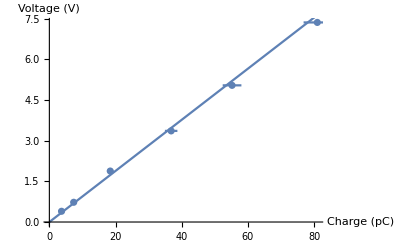

```mathematica
Show[ErrorListPlot[Table[{{chrgAmpfVoltAdjusted[[i,1]],chrgAmpfVoltAdjusted[[i,2]]},ErrorBar[δQAdjusted[[i]],δVa[[i]]]},{i,1,Length[chrgAmpfVoltAdjusted]}]],Plot[chrgAmpfVoltFit[x],{x,0,90}],AxesLabel->{"Charge (pC)","Voltage (V)"},ImageSize->Full]
```

Compare Kai squared with curve.fit

### Section A .2 : Capacitance of Parallel Plates

With our proportionality constant now stored in propConst, we can move on to the task at hand which is determining the capacitance of our parallel plates. To do this, we setup the plates at a distance d from each other and apply a constant voltage through the function generator and then measure the output voltage through the amplifier. This output voltage corresponds to a charge on the plates via our proportionality constant. We can then use the equation C = Q/V where C is the capacitance, Q is the charge on the plates, and V is the voltage applied to the plates to determine the capacitance.

```mathematica
(*Table 2*)
distVolt={{0.014,1.42},{0.033,0.564},{0.050,0.384},{0.069,0.274},{0.089,0.212},{0.109,0.172}};
invDistVolt=Table[{1/distVolt[[i,1]],distVolt[[i,2]]},{i,1,Length[distVolt]}];
(*Note that the units of charge here are Coulombs*)
invDistChrg=Table[{invDistVolt[[i,1]],invDistVolt[[i,2]]/(propConst*10^12)},{i,1,Length[invDistVolt]}];
invDistChrg//TableForm
```

71.4286 | 1.50658×10^-11
30.303 | 5.98388×10^-12
20. | 4.07413×10^-12
14.4928 | 2.90706×10^-12
11.236 | 2.24926×10^-12
9.17431 | 1.82487×10^-12

```mathematica
δV={0.02,0.004,0.004,0.004,0.002,0.002};
δd=Table[0.001,{i,1,Length[δV]}];
uncInvDistChrg=Table[{δd[[i]]/distVolt[[i,1]]^2,Sqrt[(δV[[i]]/(propConst*10^12))^2+((δPropConst*invDistVolt[[i,2]])/(propConst^2*10^12))^2]},{i,1,Length[invDistVolt]}];
δInvDist=Table[uncInvDistChrg[[i,1]],{i,1,Length[uncInvDistChrg]}];
δChrg=Table[uncInvDistChrg[[i,2]],{i,1,Length[uncInvDistChrg]}];
uncInvDistChrg//TableForm
```

5.10204 | 4.11436×10^-13
0.918274 | 1.46296×10^-13
0.4 | 1.04343×10^-13
0.21004 | 8.01706×10^-14
0.126247 | 5.6743×10^-14
0.084168 | 4.76788×10^-14

```mathematica
(*Theoretical Value*)
A=0.0043;δA=0.0002;
Vfg=20;δVfg=0.2;
theorVal=A*Vfg*8.854*10^-12;
uncTheorVal=Sqrt[(A*8.854*10^-12*δVfg)^2+(Vfg*8.854*10^-12*δA)^2];
theorVal±uncTheorVal
```

7.61444×10^-13±3.62253×10^-14

{1.99999×10^-13 x, | Estimate | Standard Error | t-Statistic | P-Value
x | 1.99999×10^-13 | 7.54585×10^-16 | 265.045 | 1.45092×10^-11}

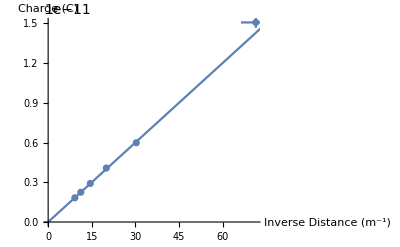

```mathematica
invDistChrgFit=LinearModelFit[invDistChrg,x,x,Weights->1/(δInvDist^2+δChrg^2),IncludeConstantBasis->False];
invDistChrgFit[{"BestFit","ParameterTable"}]
Show[ErrorListPlot[Table[{{invDistChrg[[i,1]],invDistChrg[[i,2]]},ErrorBar[δInvDist[[i]],δChrg[[i]]]},{i,1,Length[invDistChrg]}]],Plot[invDistChrgFit[x],{x,0,90}],AxesLabel->{"Inverse Distance (m^-1)","Charge (C)"},ImageSize->Full]
```

## Section B .1: Cylinder Over Grounded Plate

In this section, we are working with a cylinder of reasonably small radius (1.2 cm) suspended over a plate with a charge sensor. We will be doing something similar to Section A where we vary the separation between them and then find the charge on the sensor as a function of the separation. In this section we will also be introducing horizontal offset, x, as well.

```mathematica
r=0.012;δr=0.001;
Vfg=20;δVfg=0.2;
A=0.0043;δA=0.0002;
```

```mathematica
(*Offset of x=0*)
distVolt={{0.02,0.656},{0.04,0.320},{0.06,0.196},{0.08,0.140},{0.10,0.106},{0.12,0.086}};
δd=Table[0.001,{i,1,Length[distVolt]}];
δVa={0.008,0.008,0.002,0.002,0.002,0.001};
distVolt//TableForm
Table[{δd[[i]],δVa[[i]]},{i,1,Length[δd]}]//TableForm
```

0.02 | 0.656
0.04 | 0.32
0.06 | 0.196
0.08 | 0.14
0.1 | 0.106
0.12 | 0.086

0.001 | 0.008
0.001 | 0.008
0.001 | 0.002
0.001 | 0.002
0.001 | 0.002
0.001 | 0.001

```mathematica
(*Theoretical Value*)
theorVal=A*Vfg*8.854*10^-12;
uncTheorVal=Sqrt[(A*8.854*10^-12*δVfg)^2+(Vfg*8.854*10^-12*δA)^2];
theorVal±uncTheorVal
```